# SimPack

## External calculations with FORTRAN code - Cu

```mathematica
Needs["GroupTheory`"];
```

```mathematica
dir=NotebookDirectory[]
```

/Users/tpqhe/SVN_SimPack_New/_NEW1/examples/Cu_spd/math/

## Read ETB-Parameters and Hamiltonian

Load all data

```mathematica
SetDirectory[dir<>"../../../math"];
```

```mathematica
hfcc= GTReadFromFile["fcc_spd.ham"];
```

```mathematica
cu=GTTbDatabaseRetrieve["TB_Handbook","Cu"];
```

```mathematica
GTTbPrintParmSet["TB_Handbook","Cu"];
```

Name       : | Cu
Structure  : | fcc
Authors    : | Papaconstantopoulos
Reference  : | Handbook of the Bandstructure of Elemental Solids, Springer, 1986

(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

(ss0) | (pp0) | (dd0) | (dd1) | (dd2) | (pd0)
0.79466 | 1.35351 | 0.37 | 0.37307 | 0.3718 | 0.

## Calculations in Mathematica

### Band structure

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu];
```

calculate band structure

Maximum Abscissa = 4.48735

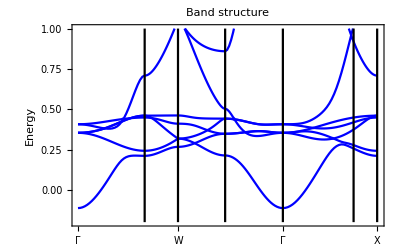

```mathematica
kp=GTBZPath["fcc"];
plt1=GTBandStructure[hfccp,kp,30,7, Joined->True,PlotStyle->Blue,PlotRange->{{0,4.5},{-.2,1}}]
```

## Calculations of bands in FORTRAN

#### Export parameters if necessary

```mathematica
SetDirectory[NotebookDirectory[]<>"../bands"]
```

/Users/tpqhe/SVN_SimPack_New/_NEW1/examples/Cu_spd/bands

```mathematica
GTTbParmExport[cu,"cu.parm","Cu parameters from Papaconstantopoulos"];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

21 | 22 | 23 | 24 | 25 | 26
(ss0) | (pp0) | (dd0) | (dd1) | (dd2) | (pd0)
0.79466 | 1.35351 | 0.37 | 0.37307 | 0.3718 | 0.

### Band structure

```mathematica
SetDirectory[dir<>"../bands"]
```

/Users/tpqhe/SVN_SimPack_new/_NEW/examples/Cu/bands

The k-vectors will exported for the FORTRAN calculation

```mathematica
kpl=GTBZLines[kp,{5,5,5,5,5,5}];GTBZTbPointMesh["kfcc.lin",kpl,5,13]
```

Use k-points in FORTRAN-ETBM calculation for Bands

Output in file    : kfcc.lin

Number of k-points: 25

kfcc.lin

Read the result of the calculation and plot the band structure.

```mathematica
bands=GTTbReadBands["bands.bnd",kpl];
```

Number of k-points : 25

Maximum Abscissa = 4.48735

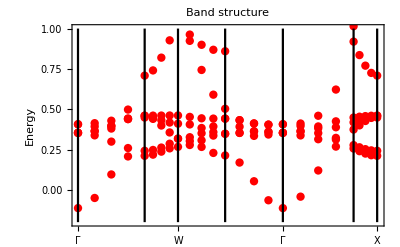

```mathematica
plt2=GTBandsPlot[bands,9,PlotRange->{{0,4.5},{-.2,1}},PlotStyle->{{Red,PointSize[0.015]}}]
```

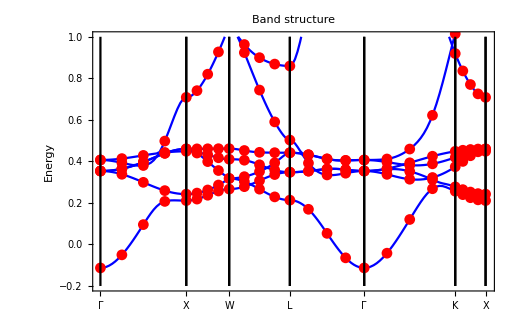

```mathematica
Show[plt1,plt2]
```

We get identical results. All is fine.